# Complex Data fitting in Mathematica

A short notebook that show how to fit data in Mathematica (if any questions, email to marco.scigliuzzo.physics@gmail.com)

### Example Function

Microwave resonators are always good proxy. Using:
ω0 resonance
κr radiative decay 
κnr non radiative decay
ω probing angular frequency

```mathematica
Clear[ω, ω0, κr, κnr]
```

Reflection configuration

```mathematica
S11=(κnr-κr+2 ⅈ (ω-ω0))/(κnr+κr+2 ⅈ (ω-ω0));
```

Notch Configuration

```mathematica
S21Notch=(κnr+2ⅈ (ω-ω0))/(κnr+κr+2ⅈ (ω-ω0));
```

Transmission Configuration

```mathematica
S21Transmission=2 Sqrt[κr1 κr2]/(κnr+κr1+κr2+2ⅈ (ω-ω0));
```

### Plot the function

```mathematica
myω0=2π 5.0;
myκr=2π 0.001;
myκr1=2π 0.001;
myκr2=2π 0.001;
myκnr=2π 0.001;
myParam={ κnr->myκnr,κr->myκr, ω0->myω0};
myParamT={ κnr->myκnr,κr1->myκr1,κr2->myκr2, ω0->myω0};
```

Reflection Configuration

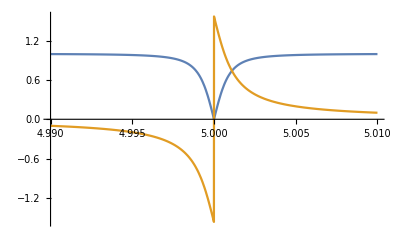

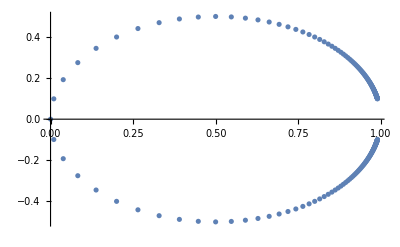

```mathematica
Plot[{Abs@S11/.myParam/.ω->2π x,Arg@S11/.myParam/.ω->2π x},{x,4.99,5.01}, PlotRange->All]
ListPlot[Table[{Re@S11/.myParam/.ω->2π x,Im@S11/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}]]
```

Notch Configuration

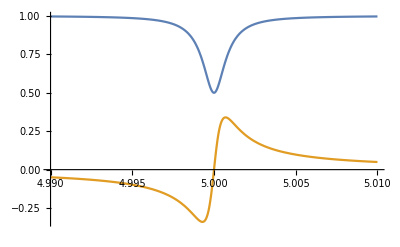

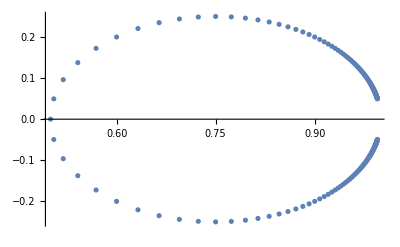

```mathematica
Plot[{Abs@S21Notch/.myParam/.ω->2π x,Arg@S21Notch/.myParam/.ω->2π x},{x,4.99,5.01}, PlotRange->All]
ListPlot[Table[{Re@S21Notch/.myParam/.ω->2π x,Im@S21Notch/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}], PlotRange->All]
```

Transmission configuration

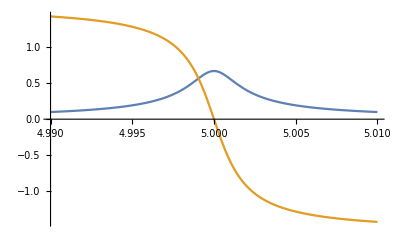

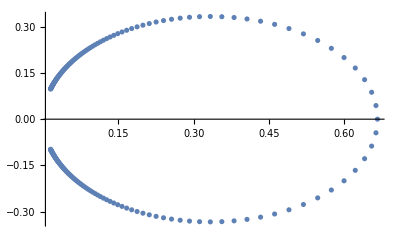

```mathematica
Plot[{Abs@S21Transmission/.myParamT/.ω->2π x,Arg@S21Transmission/.myParamT/.ω->2π x},{x,4.99,5.01}, PlotRange->All]
ListPlot[Table[{Re@S21Transmission/.myParamT/.ω->2π x,Im@S21Transmission/.myParamT/.ω->2π x},{x,4.99,5.01,0.0001}], PlotRange->All]
```

### Generating Noise data to fit

Generate some some noisy data

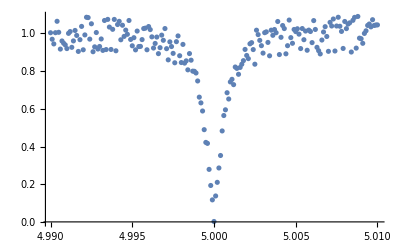

```mathematica
fitDataS11=Table[{x, Random[Complex,{-0.1,0.1}]+S11/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}];
ListPlot[Transpose@{fitDataS11[[;;,1]],Abs@fitDataS11[[;;,2]]}, PlotRange->All]
```

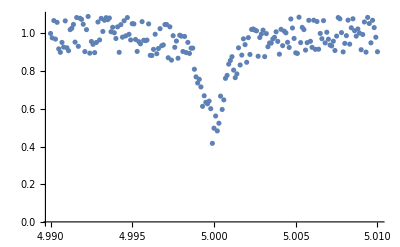

```mathematica
fitDataS21Notch=Table[{x, Random[Complex,{-0.1,0.1}]+S21Notch/.myParam/.ω->2π x},{x,4.99,5.01,0.0001}];
ListPlot[Transpose@{fitDataS21Notch[[;;,1]],Abs@fitDataS21Notch[[;;,2]]}, PlotRange->All]
```

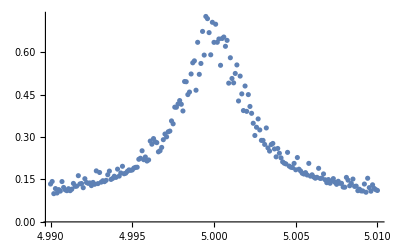

```mathematica
fitDataS21T=Table[{x, Random[Complex,{-0.1,0.1}]+S21Transmission/.myParamT/.ω->2π x},{x,4.99,5.01,0.0001}];
ListPlot[Transpose@{fitDataS21T[[;;,1]],Abs@fitDataS21T[[;;,2]]}, PlotRange->All]
```

### Complex Fit

Fit the different configurations

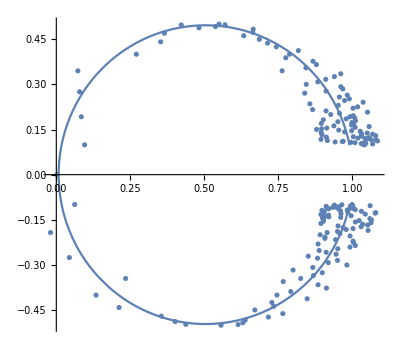

```mathematica
fitResults=FindFit[fitDataS11,S11/.ω-> 2π x,{{κr,myκr},{ω0, myω0},{κnr, myκnr}},x,NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)];
plt1=ParametricPlot[ {Re@S11, Im@S11} /. fitResults /.ω->2π x, {x,4.99,5.01}, PlotRange->All];
plt2=ListPlot[Transpose@{Re@fitDataS11[[;;,2]],Im@fitDataS11[[;;,2]]}, PlotRange->All];
Show[plt1,plt2]
```

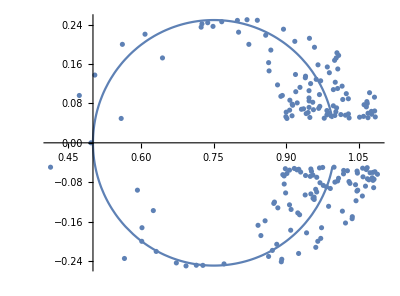

```mathematica
fitResults=FindFit[fitDataS21Notch,S21Notch/.ω-> 2π x,{{κr,myκr},{ω0, myω0},{κnr, myκnr}},x,NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)];
plt1=ParametricPlot[ {Re@S21Notch, Im@S21Notch} /. fitResults /.ω->2π x, {x,4.99,5.01}, PlotRange->All];
plt2=ListPlot[Transpose@{Re@fitDataS21Notch[[;;,2]],Im@fitDataS21Notch[[;;,2]]}, PlotRange->All];
Show[plt1,plt2]
```

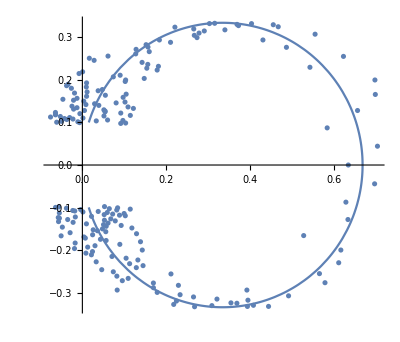

```mathematica
fitResults=FindFit[fitDataS21T,S21Transmission/.ω-> 2π x,{{κr1,myκr1},{κr2,myκr2},{ω0, myω0},{κnr, myκnr}},x,NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)];
plt1=ParametricPlot[ {Re@S21Transmission, Im@S21Transmission} /. fitResults /.ω->2π x, {x,4.99,5.01}, PlotRange->All];
plt2=ListPlot[Transpose@{Re@fitDataS21T[[;;,2]],Im@fitDataS21T[[;;,2]]}, PlotRange->All];
Show[plt1,plt2]
```